```mathematica
t=1;
a=1;
f[x_, y_, E_, λ_]:=(2 t)^2/π^3 Sin[x]^2(Im[1/(E-2t(Cos[x]-Cos[y])-I λ)])^2
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

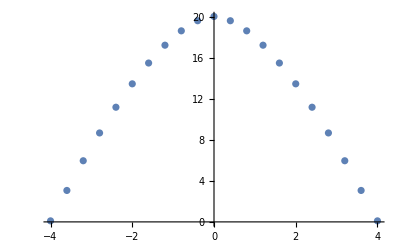

```mathematica
En=Table[i,{i,-4,4,0.4}];
σ=Table[Re[NIntegrate[f[x,y,E,0.0404],{x,-π,π},{y,-π,π}]],{E,-4,4,0.4}];
data=Transpose@{En,σ};
ListPlot[data,PlotRange->All]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"CondDC_XX.dat"}],data];
```

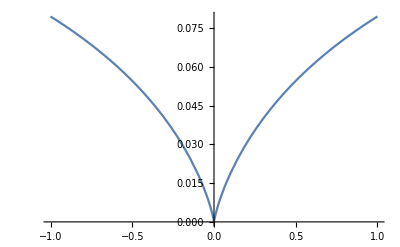

```mathematica
(*Manipulate[Plot3D[f[x,y,E,0.1],{x,-2π,2π},{y,-2π,2π},PlotRange->All,PlotPoints->100],{E,-3,3}]*)

DOS[x_,t_,a_]:=1/(2 π^2 t a^2)EllipticK[1-1/x^2]/1
Plot[DOS[x,1,1],{x,-1,1}]
```

```mathematica
t=1;
a=1;
g[e_]:=NIntegrate[1/(2 π^2 t a^2)1/(√((1-x^2)(1-(x-Abs[e])^2))),{x,-1+Abs[e],1}]
```

NIntegrate::nlim: x = -1.+Abs[e] is not a valid limit of integration.

Plot::exclul: {√((1-x^2) (1-Plus[«2»]^2))-0} must be a list of equalities or real-valued functions.

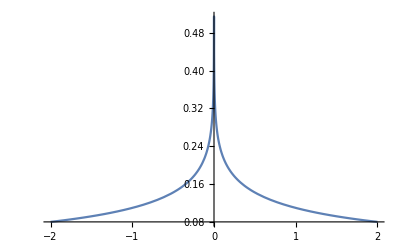

NIntegrate::zeroregion: Integration region {{1.,0.99999999999999999999999999994550487499921148932838006865794000847}} cannot be further subdivided at the specified working precision. NIntegrate assumes zero integral there and on any further indivisible regions.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.99999999999999621324610876750152937355535778527017545173720403096}. NIntegrate obtained 1.95751 and 0.0454515 for the integral and error estimates.

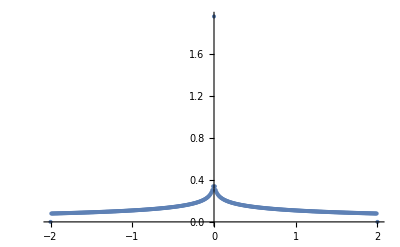

```mathematica
Plot[g[e],{e,-2,2},PlotRange->All]
En=Table[i,{i,-2,2,0.01}];
ρ=Table[g[E],{E,-2,2,0.01}];
data=Transpose@{En,ρ};
ListPlot[data,PlotRange->All]
Export[FileNameJoin[{NotebookDirectory[],"DOS.dat"}],data];
```

```mathematica
t=1/(4*1.01);
a=1;
DR[kx_, ky_]=2 t (Cos[kx a] + Cos[ky a]);
Table[Re[NIntegrate[(4(2 t)^2)/(2π)^2 ChebyshevT[n,DR[kx, ky]]/(1+KroneckerDelta[1,0])ChebyshevT[m,DR[kx, ky]]/(1+KroneckerDelta[1,0])Sin[kx]^2,{kx,0,π},{ky,0,π}]] ,{n,0,4},{m,0,4}]//MatrixForm
Table[Re[NIntegrate[4/((2π)^2 a^2)ChebyshevT[n,DR[kx, ky]]/(1+KroneckerDelta[1,0]),{kx,0,π},{ky,0,π}]] ,{n,0,10}]//MatrixForm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.31193×10^-19 and 9.05915×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.57599×10^-18 and 1.88149×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.31193×10^-19 and 9.05915×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

(0.122537 | 3.31193×10^-19 | -0.0774911 | -2.57599×10^-18 | 0.0159505
3.31193×10^-19 | 0.022523 | -6.42051×10^-19 | -0.0307703 | -1.62334×10^-18
-0.0774911 | -6.42051×10^-19 | 0.0692437 | 2.83751×10^-18 | -0.0391882
-2.57599×10^-18 | -0.0307703 | 2.83751×10^-18 | 0.0608259 | 1.29003×10^-18
0.0159505 | -1.62334×10^-18 | -0.0391882 | 1.29003×10^-18 | 0.0617921)

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.49589×10^-8 and 1.36135×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.62076×10^-17 and 1.71431×10^-14 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.62258×10^-17 and 1.0298×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

(1.
-1.49589×10^-8
-0.509852
-2.62076×10^-17
0.120511
-1.62258×10^-17
-0.131394
2.70182×10^-18
0.0665815
1.63584×10^-16
-0.0745083)